```mathematica
mxsol= Compile[{β,ω},
h=1;
tm =100;
y[t_]=({{y1[t]}, {y2[t]}});
B = ({{β, ω}, {-ω, β}});
init=y[0]=={{-1},{0}};
sol=NDSolve[N[LogicalExpand[y'[t]==B.y[t-h]&&init]],{y1,y2},{t,0,tm}];
yy1[t_]=y1[t]/.sol[[1]];
yy2[t_]=y2[t]/.sol[[1]];
FindMaximum[{√(yy1[t]^2+yy2[t]^2)&&h≤ t≤ tm},{t,h}][[1]]]
wt = Compile[{β},
th1=0.999;
dw = 0.005;
Catch[Do[If[mxsol[β,w]>th1,Throw[w]],{w,0,10,dw}]]]
```

CompiledFunction[{β,ω},h=1;tm=100;y[t_]={{y1[t]},{y2[t]}};B={{β,ω},{-ω,β}};init=y[0]=={{-1},{0}};sol=NDSolve[N[LogicalExpand[y'[t]==B.y[t-h]&&init]],{y1,y2},{t,0,tm}];yy1[t_]=y1[t]/.sol⟦1⟧;yy2[t_]=y2[t]/.sol⟦1⟧;FindMaximum[{√(yy1[t]^2+yy2[t]^2)&&h≤t≤tm},{t,h}]⟦1⟧,-CompiledCode-]

CompiledFunction[{β},th1=0.999;dw=0.005;Catch[Do[If[mxsol[β,w]>th1,Throw[w]],{w,0,10,dw}]],-CompiledCode-]

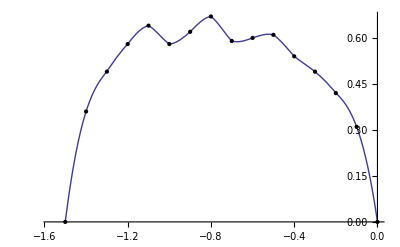

```mathematica
wt[-1.4]
data2 = Table[{β,wt[β]},{β,-1.5,0,0.1}]
ifun = Interpolation[data2];
Plot[{ifun[β]}, {β,-1.5,0}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data2]]
```

{{-1.5708,9.62076×10^-17},{-1.5608,0.0154885},{-1.5508,0.0305532},{-1.5408,0.0452149},{-1.5308,0.0594928},{-1.5208,0.0734042},{-1.5108,0.0869653},{-1.5008,0.100191},{-1.4908,0.113094},{-1.4808,0.125688},{-1.4708,0.137983},{-1.4608,0.149992},{-1.4508,0.161724},{-1.4408,0.173187},{-1.4308,0.184392},{-1.4208,0.195346},{-1.4108,0.206057},{-1.4008,0.216531},{-1.3908,0.226777},{-1.3808,0.236799},{-1.3708,0.246604},{-1.3608,0.256198},{-1.3508,0.265587},{-1.3408,0.274774},{-1.3308,0.283764},{-1.3208,0.292564},{-1.3108,0.301175},{-1.3008,0.309603},{-1.2908,0.317852},{-1.2808,0.325924},{-1.2708,0.333824},{-1.2608,0.341555},{-1.2508,0.34912},{-1.2408,0.356522},{-1.2308,0.363763},{-1.2208,0.370847},{-1.2108,0.377775},{-1.2008,0.384551},{-1.1908,0.391177},{-1.1808,0.397655},{-1.1708,0.403987},{-1.1608,0.410175},{-1.1508,0.416221},{-1.1408,0.422127},{-1.1308,0.427895},{-1.1208,0.433526},{-1.1108,0.439022},{-1.1008,0.444384},{-1.0908,0.449615},{-1.0808,0.454714},{-1.0708,0.459684},{-1.0608,0.464526},{-1.0508,0.469241},{-1.0408,0.47383},{-1.0308,0.478295},{-1.0208,0.482635},{-1.0108,0.486853},{-1.0008,0.490949},{-0.990796,0.494924},{-0.980796,0.498778},{-0.970796,0.502513},{-0.960796,0.506129},{-0.950796,0.509627},{-0.940796,0.513008},{-0.930796,0.516271},{-0.920796,0.519418},{-0.910796,0.522449},{-0.900796,0.525364},{-0.890796,0.528165},{-0.880796,0.53085},{-0.870796,0.533421},{-0.860796,0.535878},{-0.850796,0.53822},{-0.840796,0.540449},{-0.830796,0.542564},{-0.820796,0.544566},{-0.810796,0.546454},{-0.800796,0.548228},{-0.790796,0.549889},{-0.780796,0.551436},{-0.770796,0.552869},{-0.760796,0.554189},{-0.750796,0.555394},{-0.740796,0.556485},{-0.730796,0.557462},{-0.720796,0.558323},{-0.710796,0.559069},{-0.700796,0.559699},{-0.690796,0.560213},{-0.680796,0.560611},{-0.670796,0.56089},{-0.660796,0.561052},{-0.650796,0.561095},{-0.640796,0.561019},{-0.630796,0.560822},{-0.620796,0.560504},{-0.610796,0.560064},{-0.600796,0.559501},{-0.590796,0.558814},{-0.580796,0.558001},{-0.570796,0.557062},{-0.560796,0.555995},{-0.550796,0.554798},{-0.540796,0.553471},{-0.530796,0.552012},{-0.520796,0.550418},{-0.510796,0.548689},{-0.500796,0.546822},{-0.490796,0.544816},{-0.480796,0.542667},{-0.470796,0.540375},{-0.460796,0.537936},{-0.450796,0.535348},{-0.440796,0.532608},{-0.430796,0.529714},{-0.420796,0.526662},{-0.410796,0.523449},{-0.400796,0.520071},{-0.390796,0.516525},{-0.380796,0.512807},{-0.370796,0.508912},{-0.360796,0.504836},{-0.350796,0.500574},{-0.340796,0.496121},{-0.330796,0.49147},{-0.320796,0.486616},{-0.310796,0.481553},{-0.300796,0.476272},{-0.290796,0.470766},{-0.280796,0.465028},{-0.270796,0.459047},{-0.260796,0.452813},{-0.250796,0.446315},{-0.240796,0.439542},{-0.230796,0.43248},{-0.220796,0.425113},{-0.210796,0.417426},{-0.200796,0.4094},{-0.190796,0.401013},{-0.180796,0.392243},{-0.170796,0.383063},{-0.160796,0.373441},{-0.150796,0.363342},{-0.140796,0.352725},{-0.130796,0.341542},{-0.120796,0.329732},{-0.110796,0.317227},{-0.100796,0.303941},{-0.0907963,0.289763},{-0.0807963,0.274558},{-0.0707963,0.258141},{-0.0607963,0.240264},{-0.0507963,0.220573},{-0.0407963,0.198526},{-0.0307963,0.173226},{-0.0207963,0.142956},{-0.0107963,0.103437},{-0.000796327,0.0282099}}

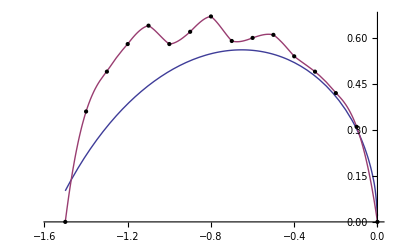

```mathematica
rehl ={{-1.5707963267948966,9.620755706465509*^-17},{-1.5607963267948965,0.015488527363793933},{-1.5507963267948965,0.030553175730054862},{-1.5407963267948965,0.04521488873230396},{-1.5307963267948965,0.059492752594556095},{-1.5207963267948965,0.0734042177388241},{-1.5107963267948965,0.08696528737654338},{-1.5007963267948965,0.10019067890796463},{-1.4907963267948965,0.11309396277624653},{-1.4807963267948965,0.12568768251210824},{-1.4707963267948965,0.13798345899410053},{-1.4607963267948965,0.1499920813904428},{-1.4507963267948965,0.1617235868052344},{-1.4407963267948967,0.17318733029818636},{-1.4307963267948967,0.18439204666283765},{-1.4207963267948966,0.19534590511848587},{-1.4107963267948966,0.2060565578842146},{-1.4007963267948966,0.2165311834505866},{-1.3907963267948966,0.2267765252389351},{-1.3807963267948966,0.23679892623438095},{-1.3707963267948966,0.24660436009249984},{-1.3607963267948966,0.25619845914768524},{-1.3507963267948966,0.2655865396910382},{-1.3407963267948966,0.27477362483496126},{-1.3307963267948966,0.283764465238877},{-1.3207963267948966,0.2925635579342334},{-1.3107963267948965,0.3011751634561308},{-1.3007963267948965,0.3096033214625812},{-1.2907963267948965,0.3178518649998698},{-1.2807963267948965,0.3259244335531223},{-1.2707963267948965,0.33382448500449774},{-1.2607963267948965,0.3415553066069946},{-1.2507963267948965,0.34912002506936496},{-1.2407963267948965,0.3565216158367586},{-1.2307963267948965,0.36376291164225916},{-1.2207963267948965,0.37084661039619504},{-1.2107963267948965,0.3777752824728726},{-1.2007963267948965,0.38455137744801254},{-1.1907963267948964,0.39117723033458535},{-1.1807963267948967,0.39765506735979683},{-1.1707963267948966,0.4039870113216247},{-1.1607963267948966,0.41017508655943713},{-1.1507963267948966,0.4162212235698046},{-1.1407963267948966,0.4221272632955595},{-1.1307963267948966,0.42789496111345027},{-1.1207963267948966,0.4335259905433033},{-1.1107963267948966,0.4390219466994437},{-1.1007963267948966,0.4443843495031727},{-1.0907963267948966,0.4496146466733587},{-1.0807963267948966,0.45471421651062405},{-1.0707963267948966,0.4596843704891898},{-1.0607963267948965,0.46452635566916256},{-1.0507963267948965,0.46924135694088637},{-1.0407963267948965,0.47383049911192754},{-1.0307963267948965,0.47829484884630763},{-1.0207963267948965,0.48263541646472113},{-1.0107963267948965,0.48685315761368375},{-1.0007963267948965,0.4909489748108205},{-0.9907963267948966,0.49492371887283465},{-0.9807963267948966,0.49877819023208175},{-0.9707963267948966,0.5025131401470977},{-0.9607963267948966,0.506129271811902},{-0.9507963267948966,0.5096272413684049},{-0.9407963267948966,0.5130076588257816},{-0.9307963267948965,0.5162710888902501},{-0.9207963267948965,0.5194180517082733},{-0.9107963267948965,0.5224490235258256},{-0.9007963267948965,0.5253644372659897},{-0.8907963267948965,0.5281646830267973},{-0.8807963267948965,0.5308501085008864},{-0.8707963267948965,0.5334210193182134},{-0.8607963267948966,0.5358776793127342},{-0.8507963267948966,0.5382203107136502},{-0.8407963267948966,0.5404490942614913},{-0.8307963267948966,0.5425641692489984},{-0.8207963267948966,0.5445656334864357},{-0.8107963267948965,0.5464535431906498},{-0.8007963267948965,0.5482279127968477},{-0.7907963267948965,0.5498887146917276},{-0.7807963267948965,0.5514358788662391},{-0.7707963267948965,0.5528692924858725},{-0.7607963267948965,0.5541887993759869},{-0.7507963267948965,0.5553941994192705},{-0.7407963267948965,0.5564852478619807},{-0.7307963267948966,0.5574616545251425},{-0.7207963267948966,0.5583230829163696},{-0.7107963267948966,0.5590691492374237},{-0.7007963267948966,0.5596994212820334},{-0.6907963267948966,0.5602134172178362},{-0.6807963267948965,0.5606106042456047},{-0.6707963267948965,0.5608903971281322},{-0.6607963267948965,0.5610521565802975},{-0.6507963267948965,0.5610951875108829},{-0.6407963267948965,0.5610187371056675},{-0.6307963267948965,0.5608219927401613},{-0.6207963267948965,0.5605040797090458},{-0.6107963267948966,0.5600640587579492},{-0.6007963267948966,0.5595009234015661},{-0.5907963267948966,0.5588135970103267},{-0.5807963267948966,0.5580009296457873},{-0.5707963267948966,0.5570616946226233},{-0.5607963267948965,0.5559945847725282},{-0.5507963267948965,0.5547982083823907},{-0.5407963267948965,0.5534710847758137},{-0.5307963267948965,0.5520116395032612},{-0.5207963267948965,0.5504181991018249},{-0.5107963267948965,0.5486889853806882},{-0.5007963267948965,0.5468221091827324},{-0.49079632679489654,0.5448155635662651},{-0.48079632679489653,0.5426672163433973},{-0.4707963267948965,0.5403748019029818},{-0.4607963267948965,0.53793591223605},{-0.45079632679489656,0.5353479870700794},{-0.44079632679489655,0.5326083030049026},{-0.43079632679489654,0.5297139615272353},{-0.42079632679489654,0.5266618757622245},{-0.4107963267948965,0.5234487557985227},{-0.4007963267948965,0.5200710923975035},{-0.3907963267948965,0.5165251388664931},{-0.38079632679489656,0.512806890839243},{-0.37079632679489655,0.5089120636629946},{-0.36079632679489654,0.5048360670387115},{-0.35079632679489653,0.5005739764972953},{-0.3407963267948965,0.49612050121715523},{-0.3307963267948965,0.4914699475939756},{-0.32079632679489656,0.48661617785747446},{-0.31079632679489655,0.4815525628866677},{-0.30079632679489654,0.47627192819713593},{-0.29079632679489653,0.47076649185117253},{-0.2807963267948965,0.4650277927613494},{-0.2707963267948965,0.4590466075023679},{-0.2607963267948965,0.452812853291259},{-0.25079632679489655,0.4463154742094767},{-0.24079632679489654,0.4395423069771791},{-0.23079632679489653,0.43247992158703974},{-0.22079632679489652,0.4251134307731269},{-0.21079632679489652,0.41742626050178083},{-0.20079632679489653,0.40939987123967225},{-0.19079632679489653,0.40101341640372334},{-0.18079632679489652,0.39224331971347626},{-0.17079632679489654,0.3830627465127004},{-0.16079632679489653,0.37344093450771654},{-0.15079632679489652,0.36334233519035836},{-0.14079632679489654,0.35272549585449225},{-0.13079632679489653,0.3415415791519796},{-0.12079632679489653,0.32973236485190077},{-0.11079632679489652,0.31722749292238794},{-0.10079632679489653,0.30394056199277636},{-0.09079632679489652,0.28976344084034444},{-0.08079632679489653,0.2745576746100078},{-0.07079632679489653,0.2581409309064587},{-0.06079632679489653,0.24026445159190918},{-0.050796326794896526,0.2205729021612645},{-0.040796326794896524,0.19852614202054883},{-0.030796326794896526,0.1732263726755596},{-0.020796326794896527,0.14295575750720493},{-0.010796326794896526,0.10343719133295229},{-0.0007963267948965253,0.02820989847162101}}
rehlfun = Interpolation[rehl];
Plot[{rehlfun[β],ifun[β]}, {β,-1.5,0}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data2]]
```

{{-1.5,0.},{-1.49,0.115},{-1.48,0.165},{-1.47,0.2},{-1.46,0.23},{-1.45,0.26},{-1.44,0.28},{-1.43,0.305},{-1.42,0.325},{-1.41,0.34},{-1.4,0.36}}

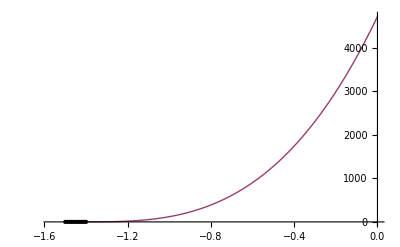

```mathematica
data3 = Table[{β,wt[β]},{β,-1.5,-1.4,0.01}]
ifun3 = Interpolation[data3];
Plot[{rehlfun[β],ifun3[β]}, {β,-1.5,0}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data3]]
```

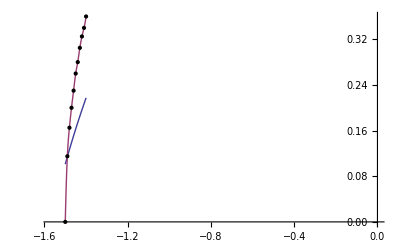

```mathematica
rehl ={{-1.5707963267948966,9.620755706465509*^-17},{-1.5607963267948965,0.015488527363793933},{-1.5507963267948965,0.030553175730054862},{-1.5407963267948965,0.04521488873230396},{-1.5307963267948965,0.059492752594556095},{-1.5207963267948965,0.0734042177388241},{-1.5107963267948965,0.08696528737654338},{-1.5007963267948965,0.10019067890796463},{-1.4907963267948965,0.11309396277624653},{-1.4807963267948965,0.12568768251210824},{-1.4707963267948965,0.13798345899410053},{-1.4607963267948965,0.1499920813904428},{-1.4507963267948965,0.1617235868052344},{-1.4407963267948967,0.17318733029818636},{-1.4307963267948967,0.18439204666283765},{-1.4207963267948966,0.19534590511848587},{-1.4107963267948966,0.2060565578842146},{-1.4007963267948966,0.2165311834505866},{-1.3907963267948966,0.2267765252389351},{-1.3807963267948966,0.23679892623438095},{-1.3707963267948966,0.24660436009249984},{-1.3607963267948966,0.25619845914768524},{-1.3507963267948966,0.2655865396910382},{-1.3407963267948966,0.27477362483496126},{-1.3307963267948966,0.283764465238877},{-1.3207963267948966,0.2925635579342334},{-1.3107963267948965,0.3011751634561308},{-1.3007963267948965,0.3096033214625812},{-1.2907963267948965,0.3178518649998698},{-1.2807963267948965,0.3259244335531223},{-1.2707963267948965,0.33382448500449774},{-1.2607963267948965,0.3415553066069946},{-1.2507963267948965,0.34912002506936496},{-1.2407963267948965,0.3565216158367586},{-1.2307963267948965,0.36376291164225916},{-1.2207963267948965,0.37084661039619504},{-1.2107963267948965,0.3777752824728726},{-1.2007963267948965,0.38455137744801254},{-1.1907963267948964,0.39117723033458535},{-1.1807963267948967,0.39765506735979683},{-1.1707963267948966,0.4039870113216247},{-1.1607963267948966,0.41017508655943713},{-1.1507963267948966,0.4162212235698046},{-1.1407963267948966,0.4221272632955595},{-1.1307963267948966,0.42789496111345027},{-1.1207963267948966,0.4335259905433033},{-1.1107963267948966,0.4390219466994437},{-1.1007963267948966,0.4443843495031727},{-1.0907963267948966,0.4496146466733587},{-1.0807963267948966,0.45471421651062405},{-1.0707963267948966,0.4596843704891898},{-1.0607963267948965,0.46452635566916256},{-1.0507963267948965,0.46924135694088637},{-1.0407963267948965,0.47383049911192754},{-1.0307963267948965,0.47829484884630763},{-1.0207963267948965,0.48263541646472113},{-1.0107963267948965,0.48685315761368375},{-1.0007963267948965,0.4909489748108205},{-0.9907963267948966,0.49492371887283465},{-0.9807963267948966,0.49877819023208175},{-0.9707963267948966,0.5025131401470977},{-0.9607963267948966,0.506129271811902},{-0.9507963267948966,0.5096272413684049},{-0.9407963267948966,0.5130076588257816},{-0.9307963267948965,0.5162710888902501},{-0.9207963267948965,0.5194180517082733},{-0.9107963267948965,0.5224490235258256},{-0.9007963267948965,0.5253644372659897},{-0.8907963267948965,0.5281646830267973},{-0.8807963267948965,0.5308501085008864},{-0.8707963267948965,0.5334210193182134},{-0.8607963267948966,0.5358776793127342},{-0.8507963267948966,0.5382203107136502},{-0.8407963267948966,0.5404490942614913},{-0.8307963267948966,0.5425641692489984},{-0.8207963267948966,0.5445656334864357},{-0.8107963267948965,0.5464535431906498},{-0.8007963267948965,0.5482279127968477},{-0.7907963267948965,0.5498887146917276},{-0.7807963267948965,0.5514358788662391},{-0.7707963267948965,0.5528692924858725},{-0.7607963267948965,0.5541887993759869},{-0.7507963267948965,0.5553941994192705},{-0.7407963267948965,0.5564852478619807},{-0.7307963267948966,0.5574616545251425},{-0.7207963267948966,0.5583230829163696},{-0.7107963267948966,0.5590691492374237},{-0.7007963267948966,0.5596994212820334},{-0.6907963267948966,0.5602134172178362},{-0.6807963267948965,0.5606106042456047},{-0.6707963267948965,0.5608903971281322},{-0.6607963267948965,0.5610521565802975},{-0.6507963267948965,0.5610951875108829},{-0.6407963267948965,0.5610187371056675},{-0.6307963267948965,0.5608219927401613},{-0.6207963267948965,0.5605040797090458},{-0.6107963267948966,0.5600640587579492},{-0.6007963267948966,0.5595009234015661},{-0.5907963267948966,0.5588135970103267},{-0.5807963267948966,0.5580009296457873},{-0.5707963267948966,0.5570616946226233},{-0.5607963267948965,0.5559945847725282},{-0.5507963267948965,0.5547982083823907},{-0.5407963267948965,0.5534710847758137},{-0.5307963267948965,0.5520116395032612},{-0.5207963267948965,0.5504181991018249},{-0.5107963267948965,0.5486889853806882},{-0.5007963267948965,0.5468221091827324},{-0.49079632679489654,0.5448155635662651},{-0.48079632679489653,0.5426672163433973},{-0.4707963267948965,0.5403748019029818},{-0.4607963267948965,0.53793591223605},{-0.45079632679489656,0.5353479870700794},{-0.44079632679489655,0.5326083030049026},{-0.43079632679489654,0.5297139615272353},{-0.42079632679489654,0.5266618757622245},{-0.4107963267948965,0.5234487557985227},{-0.4007963267948965,0.5200710923975035},{-0.3907963267948965,0.5165251388664931},{-0.38079632679489656,0.512806890839243},{-0.37079632679489655,0.5089120636629946},{-0.36079632679489654,0.5048360670387115},{-0.35079632679489653,0.5005739764972953},{-0.3407963267948965,0.49612050121715523},{-0.3307963267948965,0.4914699475939756},{-0.32079632679489656,0.48661617785747446},{-0.31079632679489655,0.4815525628866677},{-0.30079632679489654,0.47627192819713593},{-0.29079632679489653,0.47076649185117253},{-0.2807963267948965,0.4650277927613494},{-0.2707963267948965,0.4590466075023679},{-0.2607963267948965,0.452812853291259},{-0.25079632679489655,0.4463154742094767},{-0.24079632679489654,0.4395423069771791},{-0.23079632679489653,0.43247992158703974},{-0.22079632679489652,0.4251134307731269},{-0.21079632679489652,0.41742626050178083},{-0.20079632679489653,0.40939987123967225},{-0.19079632679489653,0.40101341640372334},{-0.18079632679489652,0.39224331971347626},{-0.17079632679489654,0.3830627465127004},{-0.16079632679489653,0.37344093450771654},{-0.15079632679489652,0.36334233519035836},{-0.14079632679489654,0.35272549585449225},{-0.13079632679489653,0.3415415791519796},{-0.12079632679489653,0.32973236485190077},{-0.11079632679489652,0.31722749292238794},{-0.10079632679489653,0.30394056199277636},{-0.09079632679489652,0.28976344084034444},{-0.08079632679489653,0.2745576746100078},{-0.07079632679489653,0.2581409309064587},{-0.06079632679489653,0.24026445159190918},{-0.050796326794896526,0.2205729021612645},{-0.040796326794896524,0.19852614202054883},{-0.030796326794896526,0.1732263726755596},{-0.020796326794896527,0.14295575750720493},{-0.010796326794896526,0.10343719133295229},{-0.0007963267948965253,0.02820989847162101}};
rehlfun = Interpolation[rehl];
Plot[{rehlfun[β],ifun3[β]}, {β,-1.5,-1.4}, PlotRange->{{-π/2,0}},Axes->{True,True}, Epilog->Map[Point,data3]]
```